```mathematica
FormatZykov[table_]:=Map[Factor[Simplify[{Style[SetsToLabel[#[[1]]],If[0==(#[[5]]*#[[6]])/.x->4,Red,Darker[Green]]],Factor[(#[[5]]*#[[6]])/#[[7]]],#[[5]],#[[6]],#[[7]]}]]&,table]
```

```mathematica
GreenRedPoly[poly_]:=Style[poly,If[(poly/.x->4)==0,Red,Darker[Green]]]
```

```mathematica
TableWithTotal[table_]:=TableForm[Append[
Map[{#[[1]],#[[2]]//GreenRedPoly,#[[3]]//GreenRedPoly,#[[4]]//GreenRedPoly,#[[5]]//GreenRedPoly}&,table],Prepend[Map[Style[#,Bold]&,Factor[Simplify[Total[Map[Rest,table]]]]],""]],TableHeadings->{None, {"sol","result","left","right","middle"}}]
```

```mathematica
MakeCycle[g_]:=Block[{done=True,result=g,vert=Select[VertexList[g],VertexDegree[g,#]>2&]},
vert=Sort[Select[VertexList[result],VertexDegree[result,#]>2&],VertexDegree[result,#1]>VertexDegree[result,#2]&];
While [vert≠{},
done=False;
Table[
If[!done&&EdgeQ[result,coupl],
result=EdgeDelete[result,coupl];
done=True
]
,{coupl,Map[#[[1]]<->#[[2]]&,Subsets[vert,{2}]]}
];
vert=Sort[Select[VertexList[result],VertexDegree[result,#]>2&],VertexDegree[result,#1]>VertexDegree[result,#2]&];
];
result
]
```

```mathematica
ZykovDecomposition[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{sol,lefta,righta,middlea,ChromaticPolynomial[lefta,x],ChromaticPolynomial[righta,x],ChromaticPolynomial[middlea,x]},
{sol,sols}
]
]
```

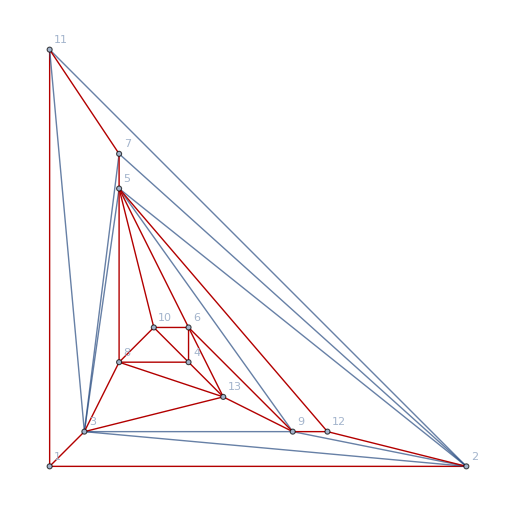

```mathematica
With[{k=10001},Graph[ReadGrof[k],VertexLabels->"Name", GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[ReadGrof[k]]]]
```

```mathematica
With[{k=10001},
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v}->Labeled[Framed[TableWithTotal[FormatZykov[ZykovDecomposition[g,adj]]]],adj]
,{v,vertices}
]
]
]
```

{{10001,8}→sol | result | left | right | middle
34♁5d♁a | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁5♁ad | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁5♁a♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
3a♁4♁5d | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3a♁45♁d | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3a♁4♁5♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
3♁4♁5d♁a | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁45♁ad | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3♁45♁a♁d | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁5♁ad | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁5♁a♁d | (-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^6 (-2+x) (-1+x) x (-17+18 x-7 x^2+x^3) | (-2+x) (-1+x) x (2-2 x+x^2){3,5,13,4,10},{10001,13}→sol | result | left | right | middle
34♁6♁89 | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁68♁9 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁6♁8♁9 | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
36♁4♁89 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
36♁49♁8 | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
36♁4♁8♁9 | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁6♁89 | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁49♁68 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3♁49♁6♁8 | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
3♁4♁68♁9 | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁6♁8♁9 | (-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^6 (-2+x) (-1+x) x (-17+18 x-7 x^2+x^3) | (-2+x) (-1+x) x (2-2 x+x^2){3,9,8,4,6},{10001,6}→sol | result | left | right | middle
49♁5d♁a | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
4♁5d♁9a | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
4♁5d♁9♁a | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
45♁9a♁d | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
45♁9♁ad | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
45♁9♁a♁d | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
49♁5♁ad | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
49♁5♁a♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
4♁5♁9a♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
4♁5♁9♁ad | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
4♁5♁9♁a♁d | (-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^6 (-2+x) (-1+x) x (-17+18 x-7 x^2+x^3) | (-2+x) (-1+x) x (2-2 x+x^2){5,9,13,4,10}}

```mathematica
With[{k=10061},
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v}->Labeled[Framed[TableWithTotal[FormatZykov[ZykovDecomposition[g,adj]]]],adj]
,{v,vertices}
]
]
]
```

{{10061,11}→sol | result | left | right | middle
17♁2d♁3 | (-3+x)^4 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-2+x) (-1+x) x
17♁2♁3♁d | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1d♁2♁37 | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (10-6 x+x^2) | (-2+x) (-1+x) x
1d♁2♁3♁7 | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2d♁37 | (-3+x)^5 (-2+x)^2 (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x)^2 (-1+x) x (13-7 x+x^2) | (-2+x) (-1+x) x
1♁2d♁3♁7 | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2♁37♁d | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
1♁2♁3♁7♁d | (-5+x) (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x (7-5 x+x^2) | (-3+x)^3 (-2+x)^2 (-1+x) x (-251+390 x-249 x^2+82 x^3-14 x^4+x^5) | (-2+x) (-1+x) x (3-3 x+x^2){1,2,3,7,13},{10061,13}→sol | result | left | right | middle
35♁7♁8b | (-3+x)^6 (-2+x) (-1+x) x (7-5 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (7-5 x+x^2) | (-2+x) (-1+x) x
35♁78♁b | (-3+x)^6 (-2+x) (-1+x) x (7-5 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (7-5 x+x^2) | (-2+x) (-1+x) x
35♁7♁8♁b | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-22+22 x-8 x^2+x^3) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (-22+22 x-8 x^2+x^3) | (-3+x) (-2+x) (-1+x) x
37♁5b♁8 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
37♁5♁8b | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-2+x) (-1+x) x
37♁5♁8♁b | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5b♁78 | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-2+x) (-1+x) x
3♁5b♁7♁8 | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5♁7♁8b | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5♁78♁b | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5♁7♁8♁b | (-5+x) (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-53+41 x-11 x^2+x^3) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-53+41 x-11 x^2+x^3) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^5 (-2+x) (-1+x) x (55-75 x+40 x^2-10 x^3+x^4) | (-2+x) (-1+x) x (2-2 x+x^2){3,11,5,7,8},{10061,10}→sol | result | left | right | middle
45♁6c♁8 | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x | (-3+x)^2 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-2+x) (-1+x) x
45♁6♁8♁c | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x
4♁5♁6c♁8 | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x
4c♁5♁6♁8 | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x
4♁5♁6♁8♁c | (-5+x) (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x)^3 (-2+x) (-1+x) x | (-3+x)^2 (-2+x)^3 (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-2+x)^3 (-1+x) x{5,6,8,4,12}}

```mathematica
ZykovSolutionCount[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
Length[FindFullFormula[middle]]
]
```

```mathematica
Table[
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v}->Labeled[ZykovSolutionCount[g,adj],adj]
,{v,vertices}
]
],{k,10000,10100}]
```

{{{10000,9}→5{2,3,5,12,6},{10000,6}→8{3,5,9,13,10},{10000,8}→8{3,5,13,4,10},{10000,13}→8{3,6,8,4,10},{10000,10}→8{5,6,8,13,4}},{{10001,8}→11{3,5,13,4,10},{10001,13}→11{3,9,8,4,6},{10001,6}→11{5,9,13,4,10}},{{10002,13}→8{5,9,6,8,10}},{{10003,8}→5{3,5,6,4,10}},{{10004,8}→5{3,5,6,4,10}},{{10005,9}→5{2,3,5,6,13},{10005,8}→5{3,5,6,4,10}},{{10006,9}→5{2,3,5,6,12},{10006,8}→5{3,5,6,4,10},{10006,10}→5{5,6,8,4,13}},{{10007,9}→5{2,3,5,6,12},{10007,10}→5{5,6,8,4,13}},{{10008,11}→5{1,2,3,13,7},{10008,9}→5{2,3,5,6,12},{10008,8}→5{3,5,6,4,10}},{{10009,11}→5{1,2,3,7,13},{10009,7}→5{2,3,11,5,13},{10009,9}→5{2,3,5,6,12},{10009,8}→5{3,5,6,4,10}},{{10010,11}→5{1,2,3,13,7},{10010,9}→5{2,3,5,6,12},{10010,8}→5{3,5,6,4,10}},{{10011,11}→5{1,2,3,7,13},{10011,7}→5{2,3,11,5,13},{10011,9}→5{2,3,5,6,12},{10011,8}→5{3,5,6,4,10}},{{10012,2}→5{1,3,11,7,13},{10012,7}→5{2,3,11,13,5},{10012,13}→5{2,3,7,5,9},{10012,8}→5{3,5,6,4,10},{10012,9}→5{3,13,5,6,12}},{{10013,2}→8{1,3,13,5,9},{10013,13}→11{1,2,11,5,7},{10013,9}→5{2,3,5,6,12},{10013,8}→5{3,5,6,4,10}},{{10014,9}→8{2,3,5,6,12},{10014,13}→8{2,3,5,7,8}},{{10015,13}→5{2,3,7,9,5},{10015,8}→5{3,5,6,4,10}},{{10016,7}→8{2,3,11,5,13},{10016,9}→8{2,3,5,6,12},{10016,13}→8{3,5,7,6,8},{10016,8}→5{5,6,13,4,10}},{{10017,7}→8{2,3,11,5,13},{10017,9}→8{2,3,5,6,12},{10017,8}→8{3,6,13,4,10},{10017,13}→11{3,5,7,8,10},{10017,10}→8{5,6,8,13,4}},{{10018,13}→11{1,3,11,5,7},{10018,9}→5{2,3,5,6,12},{10018,8}→5{3,5,6,4,10}},{{10019,11}→8{1,2,3,7,13},{10019,9}→8{2,3,5,6,12},{10019,13}→11{3,11,5,7,8}},{{10020,13}→5{3,5,9,6,8},{10020,8}→5{5,13,4,6,10}},{{10021,9}→5{2,3,5,6,12},{10021,8}→5{3,6,13,4,10},{10021,13}→5{3,5,6,8,10}},{{10022,9}→8{2,5,13,6,12},{10022,13}→11{2,3,9,8,6}},{{10023,9}→5{2,3,5,6,12},{10023,8}→8{3,5,13,4,10},{10023,13}→8{3,6,8,4,10},{10023,10}→8{5,6,8,13,4}},{{10024,8}→11{3,5,13,4,10},{10024,13}→11{3,9,8,4,6}},{{10025,9}→5{2,3,5,6,12},{10025,13}→5{5,6,8,4,10}},{{10026,2}→8{1,3,11,9,13},{10026,11}→8{1,2,3,13,7},{10026,13}→11{2,11,9,5,7},{10026,8}→5{3,5,6,4,10}},{{10027,8}→5{3,5,6,4,10}},{{10028,8}→5{3,5,6,4,10},{10028,10}→5{5,6,8,4,13}},{},{{10030,11}→5{1,2,3,7,13},{10030,7}→5{2,3,11,5,13},{10030,8}→5{3,5,6,4,10},{10030,10}→5{5,6,8,4,12}},{{10031,11}→5{1,2,3,13,7},{10031,8}→5{3,5,6,4,10},{10031,10}→5{5,6,8,4,12}},{{10032,11}→5{1,2,3,7,13},{10032,7}→5{2,3,11,5,13},{10032,8}→5{3,5,6,4,10},{10032,10}→5{5,6,8,4,12}},{{10033,2}→5{1,3,11,7,13},{10033,7}→5{2,3,11,13,5},{10033,13}→5{2,3,7,5,9},{10033,8}→5{3,5,6,4,10},{10033,10}→5{5,6,8,4,12}},{{10034,7}→8{2,3,11,13,5},{10034,13}→11{2,7,9,5,6},{10034,8}→5{3,5,6,4,10},{10034,10}→5{5,6,8,4,12}},{{10035,2}→8{1,3,13,5,9},{10035,13}→11{1,2,11,5,7},{10035,8}→5{3,5,6,4,10},{10035,10}→5{5,6,8,4,12}},{{10036,13}→8{2,3,5,7,8},{10036,10}→5{5,6,8,4,12}},{{10037,9}→5{2,3,13,5,6},{10037,13}→5{2,3,7,9,5},{10037,8}→5{3,5,6,4,10},{10037,10}→5{5,6,8,4,12}},{{10038,7}→8{2,3,11,5,13},{10038,13}→8{3,5,7,6,8},{10038,8}→5{5,6,13,4,10},{10038,10}→5{5,6,4,8,12}},{{10039,7}→8{2,3,11,5,13},{10039,8}→8{3,6,13,4,10},{10039,13}→11{3,5,7,8,10}},{{10040,11}→8{1,2,3,7,13},{10040,13}→11{3,11,5,7,8},{10040,10}→5{5,6,8,4,12}},{{10041,9}→5{2,3,5,13,6},{10041,13}→5{3,5,9,6,8},{10041,8}→5{5,13,4,6,10},{10041,10}→5{5,4,6,8,12}},{{10042,13}→11{2,3,9,8,6},{10042,10}→5{5,8,4,6,12}},{{10043,13}→5{3,5,9,8,6},{10043,10}→5{5,8,4,6,12}},{{10044,8}→8{3,5,13,4,10},{10044,13}→8{3,6,8,4,10}},{{10045,9}→8{2,3,5,13,6},{10045,8}→11{3,5,13,4,10},{10045,13}→11{3,9,8,4,6},{10045,10}→8{5,8,4,6,12}},{{10046,2}→8{1,3,11,9,13},{10046,11}→8{1,2,3,13,7},{10046,9}→8{2,3,13,5,6},{10046,13}→11{2,11,9,5,7},{10046,8}→5{3,5,6,4,10},{10046,10}→5{5,6,8,4,12}},{},{},{{10049,10}→5{5,6,8,4,13}},{{10050,11}→5{1,2,3,13,7},{10050,10}→5{5,6,8,4,12}},{{10051,11}→5{1,2,3,7,13},{10051,7}→5{2,3,11,5,13},{10051,10}→5{5,6,8,4,12}},{{10052,11}→5{1,2,3,13,7},{10052,10}→5{5,6,8,4,12}},{{10053,11}→5{1,2,3,7,13},{10053,7}→5{2,3,11,5,13},{10053,10}→5{5,6,8,4,12}},{{10054,2}→5{1,3,11,7,13},{10054,7}→5{2,3,11,13,5},{10054,13}→5{2,3,7,5,9},{10054,10}→5{5,6,8,4,12}},{{10055,7}→8{2,3,11,13,5},{10055,13}→11{2,7,9,5,6},{10055,10}→5{5,6,8,4,12}},{{10056,2}→8{1,3,13,5,9},{10056,13}→11{1,2,11,5,7},{10056,10}→5{5,6,8,4,12}},{{10057,13}→8{2,3,5,7,8},{10057,10}→5{5,6,8,4,12}},{{10058,9}→5{2,3,13,5,6},{10058,13}→5{2,3,7,9,5},{10058,10}→5{5,6,8,4,12}},{{10059,7}→8{2,3,11,5,13},{10059,13}→8{3,5,7,6,8},{10059,10}→5{5,6,4,8,12}},{{10060,13}→11{1,3,11,5,7},{10060,10}→5{5,6,8,4,12}},{{10061,11}→8{1,2,3,7,13},{10061,13}→11{3,11,5,7,8},{10061,10}→5{5,6,8,4,12}},{{10062,9}→5{2,3,5,13,6},{10062,13}→5{3,5,9,6,8},{10062,10}→5{5,4,6,8,12}},{{10063,13}→11{2,3,9,8,6},{10063,10}→5{5,8,4,6,12}},{{10064,13}→5{3,5,9,8,6},{10064,6}→5{5,8,13,4,10},{10064,10}→5{5,8,4,6,12}},{{10065,6}→8{3,5,9,13,10},{10065,13}→8{3,6,8,4,10}},{{10066,9}→8{2,3,5,13,6},{10066,13}→11{3,9,8,4,6},{10066,6}→11{5,9,13,4,10},{10066,10}→8{5,8,4,6,12}},{{10067,2}→8{1,3,11,9,13},{10067,11}→8{1,2,3,13,7},{10067,9}→8{2,3,13,5,6},{10067,13}→11{2,11,9,5,7},{10067,10}→5{5,6,8,4,12}},{{10068,13}→11{2,5,9,6,10}},{{10069,1}→5{2,3,11,12,13},{10069,8}→5{3,5,6,4,10}},{{10070,1}→5{2,3,11,12,13},{10070,11}→5{1,2,3,13,7},{10070,8}→5{3,5,6,4,10}},{{10071,7}→5{2,3,11,5,13},{10071,8}→5{3,5,6,4,10}},{{10072,1}→5{2,3,11,12,13},{10072,8}→5{3,5,6,4,10}},{{10073,7}→5{2,3,11,5,13},{10073,8}→5{3,5,6,4,10}},{{10074,11}→5{1,2,3,12,7},{10074,7}→5{2,3,11,13,5},{10074,13}→5{2,3,7,5,9},{10074,8}→5{3,5,6,4,10}},{{10075,11}→5{1,2,3,12,7},{10075,7}→8{2,3,11,13,5},{10075,13}→11{2,7,9,5,6},{10075,8}→5{3,5,6,4,10}},{{10076,11}→5{1,2,3,12,7},{10076,13}→8{2,3,5,7,8}},{{10077,11}→5{1,2,3,12,7},{10077,9}→5{2,3,13,5,6},{10077,13}→5{2,3,7,9,5},{10077,8}→5{3,5,6,4,10}},{{10078,11}→5{1,2,3,12,7},{10078,7}→8{2,3,11,5,13},{10078,13}→8{3,5,7,6,8},{10078,8}→5{5,6,13,4,10}},{{10079,11}→5{1,2,3,12,7},{10079,7}→8{2,3,11,5,13},{10079,8}→8{3,6,13,4,10},{10079,13}→11{3,5,7,8,10},{10079,10}→8{5,6,8,13,4}},{{10080,1}→8{2,3,11,12,13},{10080,11}→8{1,2,12,13,7},{10080,13}→11{1,3,11,5,7},{10080,8}→5{3,5,6,4,10}},{{10081,13}→11{3,11,5,7,8}},{{10082,11}→5{1,2,3,12,7},{10082,9}→5{2,3,5,13,6},{10082,13}→5{3,5,9,6,8},{10082,8}→5{5,13,4,6,10}},{{10083,11}→5{1,2,3,12,7},{10083,8}→5{3,6,13,4,10},{10083,13}→5{3,5,6,8,10}},{{10084,11}→5{1,2,3,12,7},{10084,13}→11{2,3,9,8,6}},{{10085,11}→5{1,2,3,12,7},{10085,13}→5{3,5,9,8,6},{10085,6}→5{5,8,13,4,10}},{{10086,11}→5{1,2,3,12,7},{10086,6}→8{3,5,9,13,10},{10086,8}→8{3,5,13,4,10},{10086,13}→8{3,6,8,4,10},{10086,10}→8{5,6,8,13,4}},{{10087,11}→5{1,2,3,12,7},{10087,9}→8{2,3,5,13,6},{10087,8}→11{3,5,13,4,10},{10087,13}→11{3,9,8,4,6},{10087,6}→11{5,9,13,4,10}},{{10088,9}→8{2,3,13,5,6},{10088,13}→11{2,11,9,5,7},{10088,8}→5{3,5,6,4,10}},{{10089,11}→5{1,2,3,12,7},{10089,13}→11{2,5,9,6,10},{10089,8}→8{3,5,6,4,10},{10089,10}→8{5,13,6,8,4}},{{10090,11}→5{1,2,3,12,7},{10090,9}→8{2,3,5,6,13},{10090,13}→8{5,9,6,8,10}},{{10091,8}→5{3,5,6,4,10}},{{10092,7}→5{2,3,11,5,13},{10092,8}→5{3,5,6,4,10}},{{10093,11}→5{1,2,3,7,13},{10093,8}→5{3,5,6,4,10}},{{10094,7}→5{2,3,11,5,12},{10094,8}→5{3,5,6,4,10}},{{10095,8}→5{3,5,6,4,10}},{{10096,11}→5{1,2,3,7,12},{10096,13}→5{2,3,7,5,9},{10096,8}→5{3,5,6,4,10}},{{10097,11}→5{1,2,3,7,12},{10097,13}→11{2,7,9,5,6},{10097,8}→5{3,5,6,4,10}},{{10098,11}→5{1,2,3,7,12},{10098,7}→5{2,3,11,12,13},{10098,13}→8{2,3,5,7,8}},{{10099,11}→5{1,2,3,7,12},{10099,7}→5{2,3,11,12,13},{10099,9}→5{2,3,13,5,6},{10099,13}→5{2,3,7,9,5},{10099,8}→5{3,5,6,4,10}},{{10100,11}→5{1,2,3,7,12},{10100,13}→8{3,5,7,6,8},{10100,8}→5{5,6,13,4,10}}}

```mathematica
10061
```

10061

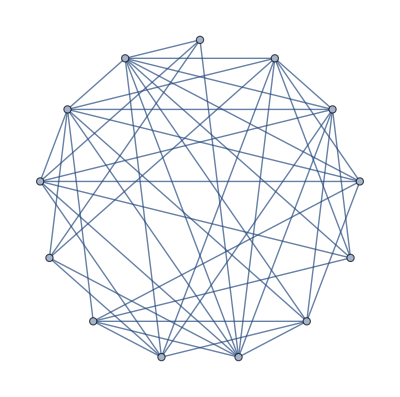

```mathematica
GraphComplement[ReadGrof[10061]]
```

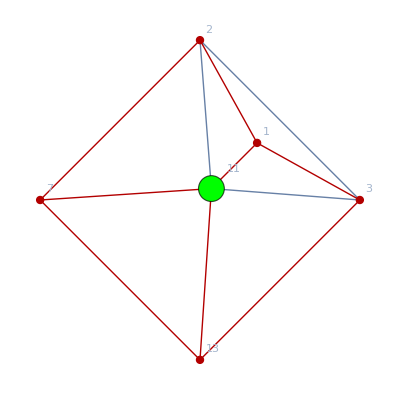
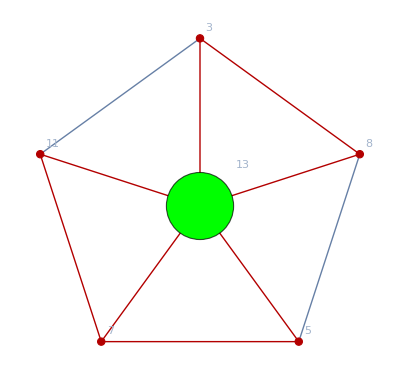
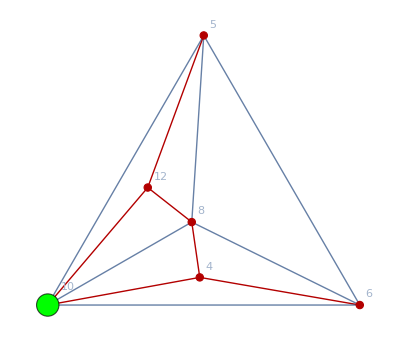
{{10061,11,-Graphics-}→sol | result | left | right | middle
17♁2d♁3 | (-3+x)^4 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-2+x) (-1+x) x
17♁2♁3♁d | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1d♁2♁37 | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (10-6 x+x^2) | (-2+x) (-1+x) x
1d♁2♁3♁7 | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2d♁37 | (-3+x)^5 (-2+x)^2 (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x)^2 (-1+x) x (13-7 x+x^2) | (-2+x) (-1+x) x
1♁2d♁3♁7 | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (103-124 x+57 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2♁37♁d | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
1♁2♁3♁7♁d | (-5+x) (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (145-159 x+67 x^2-13 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x (7-5 x+x^2) | (-3+x)^3 (-2+x)^2 (-1+x) x (-251+390 x-249 x^2+82 x^3-14 x^4+x^5) | (-2+x) (-1+x) x (3-3 x+x^2){(-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),{1,2,3,7,13},8},{10061,13,-Graphics-}→sol | result | left | right | middle
35♁7♁8b | (-3+x)^6 (-2+x) (-1+x) x (7-5 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (7-5 x+x^2) | (-2+x) (-1+x) x
35♁78♁b | (-3+x)^6 (-2+x) (-1+x) x (7-5 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (7-5 x+x^2) | (-2+x) (-1+x) x
35♁7♁8♁b | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-22+22 x-8 x^2+x^3) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (-22+22 x-8 x^2+x^3) | (-3+x) (-2+x) (-1+x) x
37♁5b♁8 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
37♁5♁8b | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-2+x) (-1+x) x
37♁5♁8♁b | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5b♁78 | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-2+x) (-1+x) x
3♁5b♁7♁8 | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5♁7♁8b | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5♁78♁b | (-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁5♁7♁8♁b | (-5+x) (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-53+41 x-11 x^2+x^3) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^5 (-2+x) (-1+x) x (-53+41 x-11 x^2+x^3) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^5 (-2+x) (-1+x) x (55-75 x+40 x^2-10 x^3+x^4) | (-2+x) (-1+x) x (2-2 x+x^2){(-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),{3,11,5,7,8},11},{10061,10,-Graphics-}→sol | result | left | right | middle
45♁6c♁8 | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x | (-3+x)^2 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-2+x) (-1+x) x
45♁6♁8♁c | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x
4♁5♁6c♁8 | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x
4c♁5♁6♁8 | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x) (-2+x) (-1+x) x
4♁5♁6♁8♁c | (-5+x) (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-3+x)^3 (-2+x) (-1+x) x | (-3+x)^2 (-2+x)^3 (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) | (-2+x)^3 (-1+x) x{(-3+x)^5 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),{5,6,8,4,12},5}}

```mathematica
With[{k=10061},
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v,Subgraph[Graph[g,GraphHighlight->Join[adj,CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexStyle->{v->Green},VertexSize->{v->Large}],Append[adj,v],GraphLayout->"TutteEmbedding"]}->Labeled[Framed[TableWithTotal[FormatZykov[ZykovDecomposition[g,adj]]]],{Factor[ChromaticPolynomial[g,x]],adj,ZykovSolutionCount[g,adj]}]
,{v,vertices}
]
]
]
```

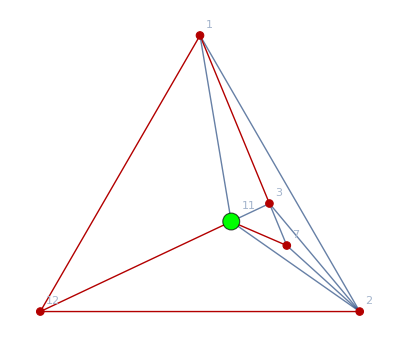
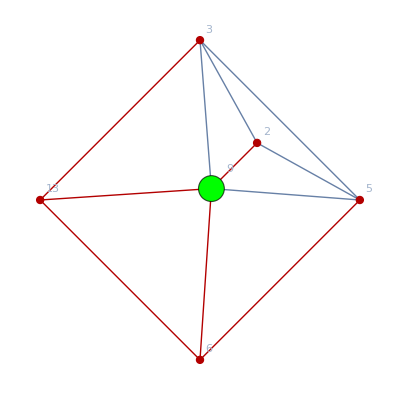
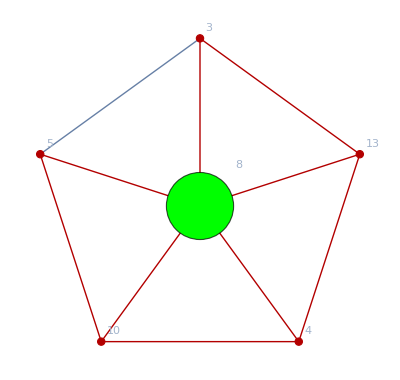
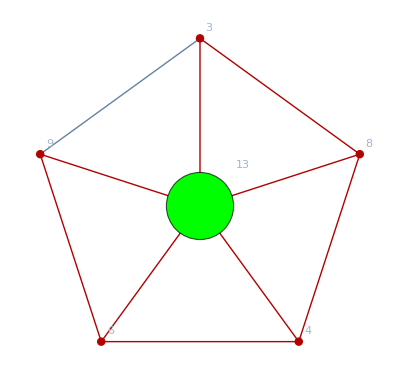
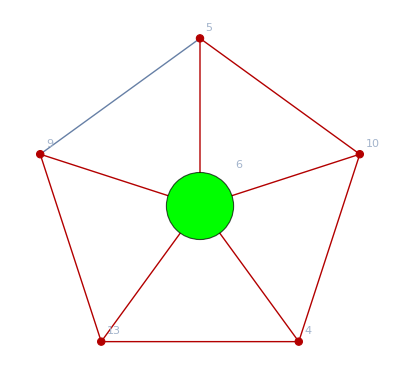
{{10087,11,-Graphics-}→sol | result | left | right | middle
17♁2♁3c | (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x | (-3+x)^3 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-2+x) (-1+x) x
17♁2♁3♁c | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2♁3c♁7 | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2♁3♁7c | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x
1♁2♁3♁7♁c | (-5+x) (-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x)^3 (-2+x) (-1+x) x | (-3+x)^3 (-2+x)^3 (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-2+x)^3 (-1+x) x{(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{1,2,3,12,7},5},{10087,9,-Graphics-}→sol | result | left | right | middle
2d♁36♁5 | (-3+x)^7 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x)^2 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x)^5 (-2+x) (-1+x) x | (-2+x) (-1+x) x
2d♁3♁5♁6 | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x (15-7 x+x^2) | (-4+x) (-3+x)^2 (-2+x) (-1+x) x (15-7 x+x^2) | (-4+x) (-3+x)^5 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
26♁3♁5d | (-3+x)^7 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x)^2 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x)^5 (-2+x) (-1+x) x | (-2+x) (-1+x) x
26♁3♁5♁d | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x (15-7 x+x^2) | (-4+x) (-3+x)^2 (-2+x) (-1+x) x (15-7 x+x^2) | (-4+x) (-3+x)^5 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
2♁36♁5d | (-4+x) (-3+x)^7 (-2+x)^2 (-1+x) x | (-4+x) (-3+x)^2 (-2+x)^2 (-1+x) x | (-3+x)^5 (-2+x) (-1+x) x | (-2+x) (-1+x) x
2♁36♁5♁d | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x)^2 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x)^5 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
2♁3♁5d♁6 | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x)^2 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x)^5 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
2♁3♁5♁6♁d | (-5+x)^2 (-4+x) (-3+x)^6 (-2+x) (-1+x) x (15-7 x+x^2) | (-5+x) (-4+x) (-3+x)^2 (-2+x) (-1+x) x (15-7 x+x^2) | (-5+x) (-4+x) (-3+x)^5 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (-745+907 x-460 x^2+122 x^3-17 x^4+x^5) | (-3+x)^2 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x)^5 (-2+x) (-1+x) x (7-5 x+x^2) | (-2+x) (-1+x) x (3-3 x+x^2){(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{2,3,5,13,6},8},{10087,8,-Graphics-}→sol | result | left | right | middle
34♁5d♁a | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁5♁ad | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁5♁a♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
3a♁4♁5d | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3a♁45♁d | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3a♁4♁5♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
3♁4♁5d♁a | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁45♁ad | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3♁45♁a♁d | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁5♁ad | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁5♁a♁d | (-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^6 (-2+x) (-1+x) x (-17+18 x-7 x^2+x^3) | (-2+x) (-1+x) x (2-2 x+x^2){(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{3,5,13,4,10},11},{10087,13,-Graphics-}→sol | result | left | right | middle
34♁6♁89 | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁68♁9 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
34♁6♁8♁9 | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
36♁4♁89 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
36♁49♁8 | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
36♁4♁8♁9 | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁6♁89 | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁49♁68 | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
3♁49♁6♁8 | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
3♁4♁68♁9 | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
3♁4♁6♁8♁9 | (-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^6 (-2+x) (-1+x) x (-17+18 x-7 x^2+x^3) | (-2+x) (-1+x) x (2-2 x+x^2){(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{3,9,8,4,6},11},{10087,6,-Graphics-}→sol | result | left | right | middle
49♁5d♁a | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
4♁5d♁9a | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
4♁5d♁9♁a | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2) | (-3+x) (-2+x) (-1+x) x
45♁9a♁d | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
45♁9♁ad | (-3+x)^8 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x)^7 (-2+x) (-1+x) x | (-2+x) (-1+x) x
45♁9♁a♁d | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
49♁5♁ad | (-4+x) (-3+x)^7 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x | (-2+x) (-1+x) x
49♁5♁a♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
4♁5♁9a♁d | (-4+x)^3 (-3+x)^6 (-2+x) (-1+x) x | (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x
4♁5♁9♁ad | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2) | (-3+x) (-2+x) (-1+x) x
4♁5♁9♁a♁d | (-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x | (-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2) | (-4+x) (-3+x) (-2+x) (-1+x) x
 | (-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4) | (-3+x) (-2+x) (-1+x) x (5-4 x+x^2) | (-3+x)^6 (-2+x) (-1+x) x (-17+18 x-7 x^2+x^3) | (-2+x) (-1+x) x (2-2 x+x^2){(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{5,9,13,4,10},11}}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
{Style[k,If[OddQ[k],Blue,Purple]],v,Subgraph[Graph[g,GraphHighlight->Join[adj,CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexStyle->{v->Green},VertexSize->{v->Large}],Append[adj,v],GraphLayout->"TutteEmbedding"]}->Labeled[Framed[TableWithTotal[FormatZykov[ZykovDecomposition[g,adj]]]],{Factor[ChromaticPolynomial[g,x]],adj,ZykovSolutionCount[g,adj]}]
,{v,vertices}
]
]
]
```

```mathematica
Flatten[{{4}, {5}, {9}, {10}, {13}}]
```

{4,5,9,10,13}

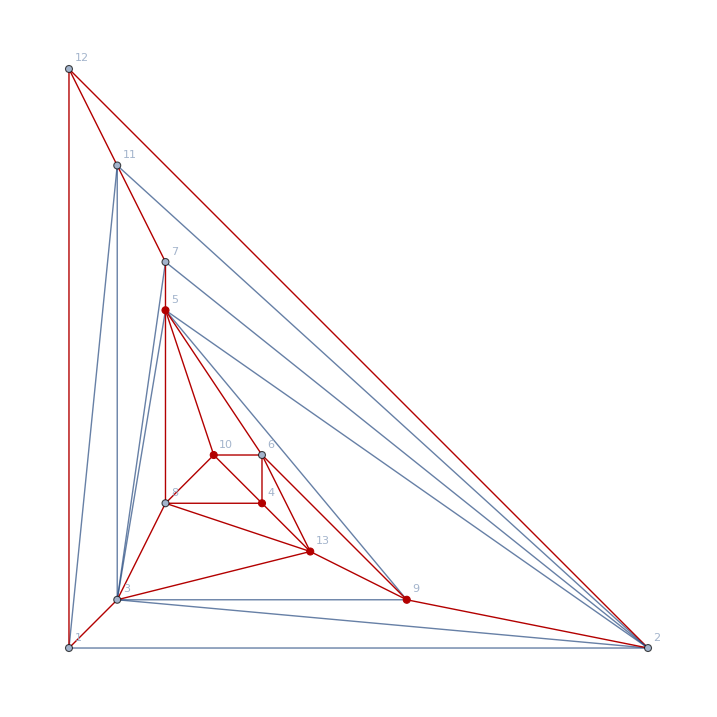

```mathematica
With[{g=ReadGrof[10087]},Graph[g,GraphHighlight->Join[{4,5,9,10,13},CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]]
```

```mathematica
ZykovDecomposition23[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200,GraphLayout->"LayeredDigraphEmbedding"];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200,GraphLayout->"LayeredDigraphEmbedding"];
{sol,lefta//GraphWithChrom,righta//GraphWithChrom,middlea//GraphWithChrom,ChromaticPolynomial[lefta,x]//Factor,ChromaticPolynomial[righta,x]//Factor,ChromaticPolynomial[middlea,x]//Factor,FindFullFormula1234[lefta],FindFullFormula1234[righta],FindFullFormula1234[middlea]},
{sol,sols}
]
]
```

```mathematica
0
```

0

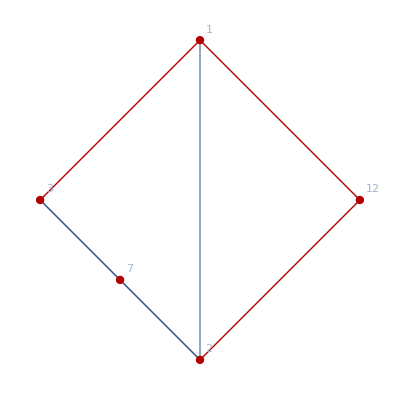
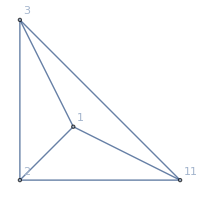
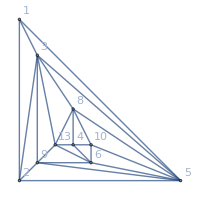
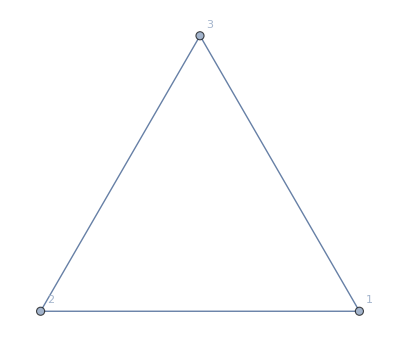
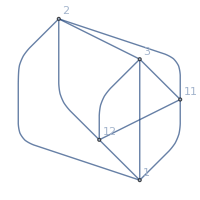
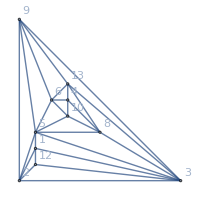
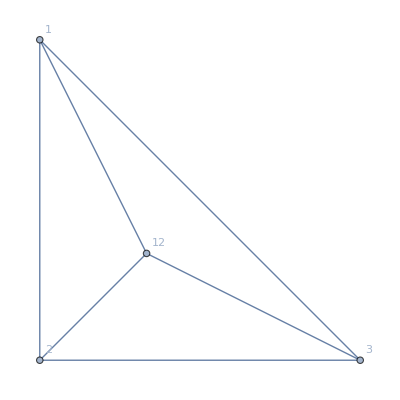
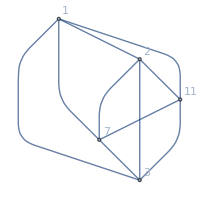
{10087,v,-Graphics-}→{{{{1,7},{2},{3,12}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^3 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^3 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-2+x) (-1+x) x,{v1x2x3xb},{v189x2adx36x45,v19ax268x34x5d,v149x268x3ax5d},{v1x2x3}},{{{1,7},{2},{3},{12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v189x2adx36x45c,v149x268x3ax5cd,v19ax268x34x5cd},{v1x2x3xc}},{{{1},{2},{3,12},{7}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v145x2adx36x789,v15dx268x3ax479,v15dx268x34x79a},{v1x2x3x7}},{{{1},{2},{3},{7,12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v145x2adx36x789,v15dx268x3ax479,v15dx268x34x79a},{v1x2x3x7}},{{{1},{2},{3},{7},{12}},-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x) (-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),0},-Graphics-{(-4+x) (-3+x) (-2+x),0},(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}{(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{1,2,3,12,7},5}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k],vertices, adj},
vertices={1,2,3,12,7};
adj={1,2,3,12,7};
{Style[k,If[OddQ[k],Blue,Purple]],v,Subgraph[Graph[g,GraphHighlight->Join[adj,CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexStyle->{v->Green},VertexSize->{v->Large}],Append[adj,v],GraphLayout->"TutteEmbedding"]}->Labeled[Framed[ZykovDecomposition23[g,vertices]],{Factor[ChromaticPolynomial[g,x]],adj,ZykovSolutionCount[g,adj]}]
]
]
```

```mathematica
ZykovDecomposition23[ReadGrof[10087],{1,2,3,12,7}]
```

{{{{1,7},{2},{3,12}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^3 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^3 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-2+x) (-1+x) x,{v1x2x3xb},{v189x2adx36x45,v19ax268x34x5d,v149x268x3ax5d},{v1x2x3}},{{{1,7},{2},{3},{12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v189x2adx36x45c,v149x268x3ax5cd,v19ax268x34x5cd},{v1x2x3xc}},{{{1},{2},{3,12},{7}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v145x2adx36x789,v15dx268x3ax479,v15dx268x34x79a},{v1x2x3x7}},{{{1},{2},{3},{7,12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v145x2adx36x789,v15dx268x3ax479,v15dx268x34x79a},{v1x2x3x7}},{{{1},{2},{3},{7},{12}},-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x) (-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),0},-Graphics-{(-4+x) (-3+x) (-2+x),0},(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}

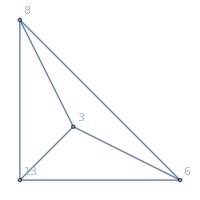
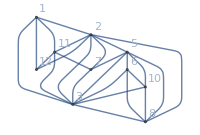
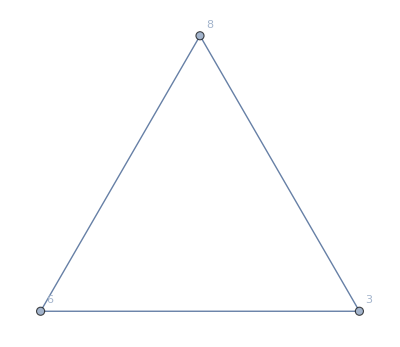
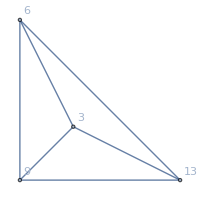
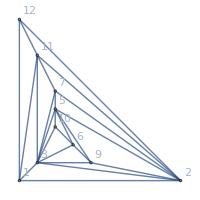
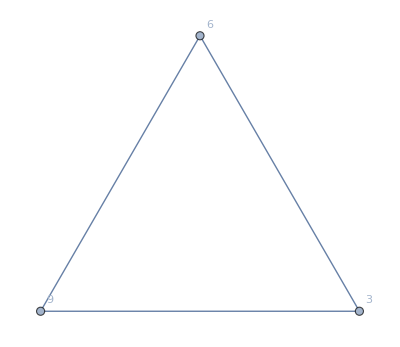
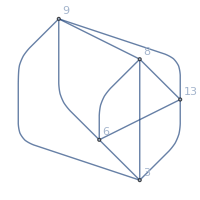
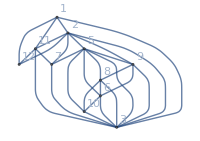
{{{{3,4},{6},{8,9}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x6x8xd},{},{v3x6x8}},{{{3,4},{6,8},{9}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^7 (-2+x),24},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^7 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x6x9xd},{v179ax26x3cx5b},{v3x6x9}},{{{3,4},{6},{8},{9}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{},{},{v3x6x8x9}},{{{3,6},{4},{8,9}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^7 (-2+x),24},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^7 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x4x8xd},{v178x2ax3cx45b},{v3x4x8}},{{{3,6},{4,9},{8}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x4x8xd},{},{v3x4x8}},{{{3,6},{4},{8},{9}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2),(-3+x) (-2+x) (-1+x) x,{},{v179ax28x3cx45b},{v3x4x8x9}},{{{3},{4},{6},{8,9}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x (13-7 x+x^2),(-3+x) (-2+x) (-1+x) x,{},{v178x26x3acx45b},{v3x4x6x8}},{{{3},{4,9},{6,8}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^7 (-2+x),24},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^7 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x4x6xd},{v147x26x3acx5b},{v3x4x6}},{{{3},{4,9},{6},{8}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{},{},{v3x4x6x8}},{{{3},{4},{6,8},{9}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^6 (-2+x) (10-6 x+x^2),48},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x (10-6 x+x^2),(-3+x) (-2+x) (-1+x) x,{},{v179x26x3acx45b,v179ax26x3cx45b},{v3x4x6x9}},{{{3},{4},{6},{8},{9}},-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x) (-3+x)^6 (-2+x) (17-8 x+x^2),0},-Graphics-{(-4+x) (-3+x) (-2+x),0},(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x (17-8 x+x^2),(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}

```mathematica
ZykovDecomposition23[ReadGrof[10087],{3,9,8,4,6}]
```